# Text Analysis in the Wolfram Language

Timothée Verdier - Wolfram Summer School 2017

## Text Corpus Search

## Content Frequency Analysis

## Frequency Analysis N-gram / Text Generation

## Probability Means Knowledge: A Simple Classifier

## High Level Text Analysis Tools

## Create Your Own...

## Corpus Search:

```mathematica
CorpusPath="/Applications/Mathematica.app/Contents/SystemFiles/Components/TextSearch/ExampleData/Text";
```

```mathematica
FileNames["*.txt",CorpusPath]
```

{/Applications/Mathematica.app/Contents/SystemFiles/Components/TextSearch/ExampleData/Text/AeneidEnglish.txt,/Applications/Mathematica.app/Contents/SystemFiles/Components/TextSearch/ExampleData/Text/AliceInWonderland.txt,/Applications/Mathematica.app/Contents/SystemFiles/Components/TextSearch/ExampleData/Text/LoremIpsum.txt,/Applications/Mathematica.app/Contents/SystemFiles/Components/TextSearch/ExampleData/Text/OriginOfSpecies.txt,/Applications/Mathematica.app/Contents/SystemFiles/Components/TextSearch/ExampleData/Text/UNHumanRightsEnglish.txt}

```mathematica
FindList[FileNames["*.txt",CorpusPath],"rabbit", 5]
```

{across her mind that she had never before seen a rabbit with either a,rabbit-hole, under the hedge. In another moment, down went Alice after it! The,rabbit-hole went straight on like a tunnel for some way and then dipped suddenly,freely under the most unnatural conditions (for instance, the rabbit and ferret,wild Indian fowl (Gallus bankiva). In regard to ducks and rabbits, the breeds of}

```mathematica
Index=CreateSearchIndex[CorpusPath]
```

SearchIndexObject[…]

```mathematica
QueryResult=TextSearch[Index,"rabbit"]
(*QueryResult=TextSearch[Index,"rabbit","Association"]*)
```

SearchResultObject[…]

```mathematica
TextSearch[Index, SearchQueryString["\"which I now\""]][All]
```

{ContentObject[…]}

```mathematica
TextSearch[Index,SearchQueryString["man -animal"]][All,"Snippet"]
```

{{ people, Whereas it is essential, if man is not to be compelled to have recourse, as a last resort}}

```mathematica
TextSearch[Index, SearchQueryString["+rabbit -Alice"]][All]
```

{ContentObject[…]}

```mathematica
QueryResult[All]
```

{ContentObject[…],ContentObject[…]}

```mathematica
QueryResult[All,"Snippet"]
```

{{I--DOWN THE RABBIT-HOLE Alice was beginning to get very tired of sitting by her sister on the bank, be worth the trouble of getting up and picking the daisies, when suddenly a White Rabbit with pink eyes ran, of the way to hear the Rabbit say to itself, "Oh dear! Oh dear! I shall be too late!" But when},{ unnatural conditions (for instance, the rabbit and ferret kept in hutches), showing, the common wild Indian fowl (Gallus bankiva). In regard to ducks and rabbits, the breeds of which differ, wild duck and rabbit. The doctrine of the origin of our several domestic races from several}}

## Content Frequency Analysis

```mathematica
text = Import[QueryResult[2]["Location"]];
```

```mathematica
TextWords[QueryResult[2]]
```

{INTRODUCTION,When,on,board,H.M.S.,Beagle,as,naturalist,I,was,much,struck,with,certain,facts,in,the,distribution,of,the,inhabitants,of,South,America,and,in,the,geological,150088,gone,cycling,on,according,to,the,fixed,law,of,gravity,from,so,simple,a,beginning,endless,forms,most,beautiful,and,most,wonderful,have,been,and,are,being,evolved}
 |  |  |  |

```mathematica
words = TextWords[text]
```

{INTRODUCTION,When,on,board,H.M.S.,Beagle,as,naturalist,I,was,much,struck,with,certain,facts,in,the,distribution,of,the,inhabitants,of,South,America,and,in,the,geological,150088,gone,cycling,on,according,to,the,fixed,law,of,gravity,from,so,simple,a,beginning,endless,forms,most,beautiful,and,most,wonderful,have,been,and,are,being,evolved}
 |  |  |  |

```mathematica
(*TextCases[text, "Sentence"]*)
```

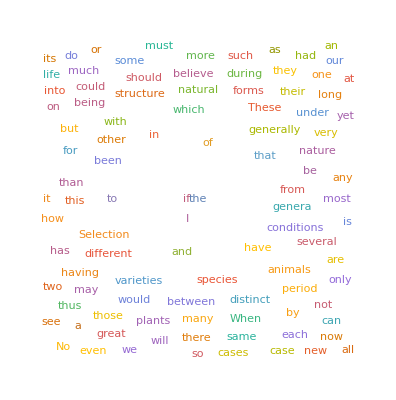

```mathematica
WordCloud[words]
```

```mathematica
topicwords = TextWords[DeleteStopwords[text]];
```

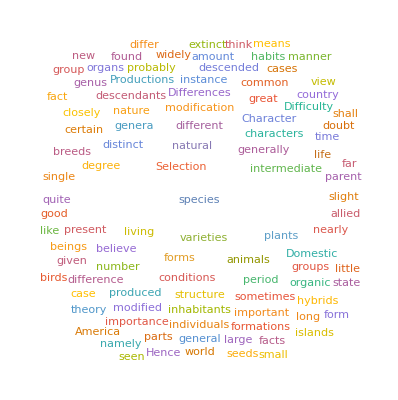

```mathematica
WordCloud[topicwords]
```

```mathematica
(*Term Frequency Inverse Document Frequency*)
```

```mathematica
WordStem[{"dogs","cats","crying","running"}]
```

{dog,cat,cry,run}

```mathematica
(N[(#/Total[#])]& @ WordCounts[DeleteStopwords[text]])[[;;10]]
```

<|species→0.0220771,forms→0.00599015,varieties→0.0059284,selection→0.00541892,natural→0.00490945,plants→0.00455437,life→0.00455437,case→0.00433823,different→0.00430735,animals→0.0042456|>

```mathematica
ClearAll[GivenWordFrequency]
GivenWordFrequency[
	text_String,
	word_String,
	chunck : _Integer?Positive : 1000, 
	pad : _Integer?Positive : 100] :=
Map[
	Count[#, ToLowerCase[word]]&,
	Partition[ToLowerCase[TextWords[DeleteStopwords[text]]], chunck, pad]
]

GivenWordFrequency[text_String, words : {__String}, rest___] := 
AssociationMap[GivenWordFrequency[text, #, rest]&, words]
```

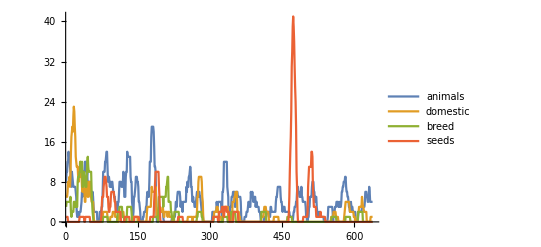

```mathematica
ListLinePlot[GivenWordFrequency[text,{"animals","domestic","breed","seeds"}],PlotRange->All]
```

## Frequency analysis n-gram / Text generation

### Markov models (N-grams)

```mathematica
m -> u -> l ->t -> i
```

```mathematica
P(Subscript[x, 1], Subscript[x, 2],..., Subscript[x, n]) = ∏_i P(Subscript[x, i] | Subscript[x, i-2], Subscript[x, i-1])
```

train by counting N-grams and (N-1)-grams.

```mathematica
P(Subscript[x, i] | Subscript[x, i-2], Subscript[x, i-1]) = Count[Subscript[x, i-2], x_(i-1,)Subscript[x, i]]/Count[Subscript[x, i-2], Subscript[x, i-1]]
```

```mathematica
P[ "multitude"] ⇒ P["m"]*P["u"\[Conditioned]"m"]*P["l" \[Conditioned]"mu"]*P["t"\[Conditioned]"mul"]*P["i"\[Conditioned]"mult"]*P["t"\[Conditioned]"multi"]*P["u"\[Conditioned]"ultit"]*P["d"\[Conditioned]"ltitu"]…
```

```mathematica
charPredictor=SequencePredict[{text},Method->{"Markov","Order"-> 5}]
```

SequencePredictorFunction[…]

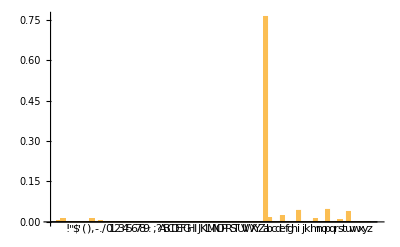

```mathematica
BarChart[Values[#],ChartLabels->Keys[#]]&@ charPredictor["anim","Probabilities"]
```

```mathematica
charPredictor["anim","NextSequence"-> 60]
```

als have been modifications of the same species of the same

```mathematica
charPredictor["anim","RandomNextElement"-> 60]
```

al, with another from it. After the warmer any one species o

```mathematica
P[ "A","multitude","of","cases"] ⇒ P[ "A"]*P[ "multitude"\[Conditioned]"A"]*P[ "of" \[Conditioned]"A","multitude"]*P[ "cases"\[Conditioned]"A","multitude","of"]
```

```mathematica
wordPredictor=SequencePredict[{text},Method->{"Markov","Order"-> 5},FeatureExtractor->"SegmentedWords"]
```

SequencePredictorFunction[…]

```mathematica
wordPredictor["animals","RandomNextElement"-> 20]
```

isolation, by a long--the
working: the imperfection

## Probability Means Knowledge: A Simple Classifier

```mathematica
Clear[SampleString]
SampleString[text_,n_]:=StringRiffle@RandomChoice[TextCases[text,"Sentence"],n]
```

```mathematica
refStr = SampleString[text,3];
spanishStr =SampleString[ExampleData[{"Text","DonQuixoteISpanish"}],3];aliceStr =SampleString[ExampleData[{"Text","AliceInWonderland"}],3];
```

```mathematica
CharMeanProba[str_]:=10^(charPredictor[str,"SequenceLogProbability"]/StringLength[str])
```

```mathematica
CharMeanProba[refStr]
CharMeanProba[spanishStr]
CharMeanProba[aliceStr]
```

0.126834

0.00033372

0.0178797

## Pretrained Classifiers

```mathematica
languageClass=Classify["Language"]
```

ClassifierFunction[…]

```mathematica
languageClass[{spanishStr,refStr}]
```

{Spanish,English}

```mathematica
topicClass=Classify["FacebookTopic"]
```

ClassifierFunction[…]

```mathematica
AMovieReviewExtract=First@RandomChoice[ExampleData[{"MachineLearning","MovieReview"},"TrainingData"]]
```

the film is ultimately about as inspiring as a hallmark card .

```mathematica
topicClass[AMovieReviewExtract]
```

Movies

```mathematica
sentimentClass = Classify["Sentiment"]
```

ClassifierFunction[…]

```mathematica
sentimentClass[AMovieReviewExtract]
```

Positive

## Content - Semantic analysis:

```mathematica
DeleteDuplicates@TextCases[text,"Country"]
```

{world,Egypt,Australia,France,Germany,Hungary,Spain,India,Iran,South Africa,United States,Ireland,Paraguay,Russia,New Zealand,China,Norway,Switzerland,Chile,Jordan,Belgium,Indian Ocean,WORLD,Brazil,World,Panama,Atlantic Ocean,Italy,Japan,Bermuda,Mauritius,Falkland Islands,Norfolk Island}

```mathematica
TextCases[text,Containing["Sentence", "Country"], 2]
```

{The argument mainly relied on by
those who believe in the multiple origin of our domestic animals is, that we
find in the most ancient records, more especially on the monuments of Egypt,
much diversity in the breeds; and that some of the breeds closely resemble,
perhaps are identical with, those still existing.,But Mr. Horner's researches have rendered it in some degree
probable that man sufficiently civilized to have manufactured pottery existed in
the valley of the Nile thirteen or fourteen thousand years ago; and who will
pretend to say how long before these ancient periods, savages, like those of
Tierra del Fuego or Australia, who possess a semi-domestic dog, may not have
existed in Egypt?}

## Grammatical analysis

```mathematica
sentences=TextSentences[text];
```

```mathematica
example = RandomChoice[sentences]
```

On the theory of natural selection
the case is especially important, inasmuch as the sterility of hybrids could not
possibly be of any advantage to them, and therefore could not have been acquired
by the continued preservation of successive profitable degrees of sterility.

```mathematica
TextStructure[example]
```

On
Preposition    the
Determinertheory
Noun
Noun Phrase  of
Preposition  natural
Adjectiveselection
Noun
Noun Phrase
Prepositional Phrase
Noun Phrase
Prepositional Phrase  the
Determinercase
Noun
Noun Phrase  is
Verb  especially
Adverbimportant
Adjective
Adjective Phrase,
Punctuation  inasmuch
Adverb
Adverb Phrase  as
Preposition      the
Determinersterility
Noun
Noun Phrase  of
Preposition  hybrids
Noun
Noun Phrase
Prepositional Phrase
Noun Phrase    could
Verbnot
Adverb  possibly
Adverb
Adverb Phrase  be
Verb  of
Preposition  any
Determineradvantage
Noun
Noun Phrase
Prepositional Phrase  to
Preposition  them
Pronoun
Noun Phrase
Prepositional Phrase
Verb Phrase
Verb Phrase,
Punctuationand
Conjunction    therefore
Adverb
Adverb Phrasecould
Verbnot
Adverb  have
Verb  been
Verb  acquired
Verb  by
Preposition    the
Determinercontinued
Verbpreservation
Noun
Noun Phrase  of
Preposition    successive
Adjectiveprofitable
Adjectivedegrees
Noun
Noun Phrase  of
Preposition  sterility
Noun
Noun Phrase
Prepositional Phrase
Noun Phrase
Prepositional Phrase
Noun Phrase
Prepositional Phrase
Verb Phrase
Verb Phrase
Verb Phrase
Verb Phrase
Verb Phrase
Clause
Clause
Verb Phrase.
Punctuation
Sentence

```mathematica
TextStructure[example,"PartsOfSpeech"]
```

On
Prepositionthe
Determinertheory
Nounof
Prepositionnatural
Adjectiveselection
Nounthe
Determinercase
Nounis
Verbespecially
Adverbimportant
Adjective,
Punctuationinasmuch
Nounas
Prepositionthe
Determinersterility
Nounof
Prepositionhybrids
Nouncould
Verbnot
Adverbpossibly
Adverbbe
Verbof
Prepositionany
Determineradvantage
Nounto
Prepositionthem
Pronoun,
Punctuationand
Conjunctiontherefore
Adverbcould
Verbnot
Adverbhave
Verbbeen
Verbacquired
Verbby
Prepositionthe
Determinercontinued
Verbpreservation
Nounof
Prepositionsuccessive
Adjectiveprofitable
Adjectivedegrees
Nounof
Prepositionsterility
Noun.
Punctuation

```mathematica
TextStructure[example,"ConstituentGraphs"]
```

{-Graphics-}

```mathematica
TextStructure[example,"ConstituentStrings"]
```

{(Sentence, ((PrepositionalPhrase, (Preposition, On), (NounPhrase, (NounPhrase, (Determiner, the), (Noun, theory)), (PrepositionalPhrase, (Preposition, of), (NounPhrase, (Adjective, natural), (Noun, selection))))), (NounPhrase, (Determiner, the), (Noun, case)), (VerbPhrase, (Verb, is), (AdjectivePhrase, (Adverb, especially), (Adjective, important)), (Punctuation, ,), (AdverbPhrase, (Adverb, inasmuch)), (Clause, (Preposition, as), (Clause, (NounPhrase, (NounPhrase, (Determiner, the), (Noun, sterility)), (PrepositionalPhrase, (Preposition, of), (NounPhrase, (Noun, hybrids)))), (VerbPhrase, (VerbPhrase, (Verb, could), (Adverb, not), (AdverbPhrase, (Adverb, possibly)), (VerbPhrase, (Verb, be), (PrepositionalPhrase, (Preposition, of), (NounPhrase, (Determiner, any), (Noun, advantage))), (PrepositionalPhrase, (Preposition, to), (NounPhrase, (Pronoun, them))))), (Punctuation, ,), (Conjunction, and), (VerbPhrase, (AdverbPhrase, (Adverb, therefore)), (Verb, could), (Adverb, not), (VerbPhrase, (Verb, have), (VerbPhrase, (Verb, been), (VerbPhrase, (Verb, acquired), (PrepositionalPhrase, (Preposition, by), (NounPhrase, (NounPhrase, (Determiner, the), (Verb, continued), (Noun, preservation)), (PrepositionalPhrase, (Preposition, of), (NounPhrase, (NounPhrase, (Adjective, successive), (Adjective, profitable), (Noun, degrees)), (PrepositionalPhrase, (Preposition, of), (NounPhrase, (Noun, sterility))))))))))))))), (Punctuation, .)))}

## Now get ready to brew your own...

```mathematica
fe=FeatureExtraction[{"The argument mainly relied on by\nthose who believe in the multiple origin of our domestic animals is, that we\nfind in the most ancient records, more especially on the monuments of Egypt,\nmuch diversity in the breeds; and that some of the breeds closely resemble,\nperhaps are identical with, those still existing."},"TFIDF"]
```

FeatureExtractorFunction[…]

```mathematica
fe["But Mr. Horner's researches have rendered it in some degree\nprobable that man sufficiently civilized to have manufactured pottery existed in\nthe valley of the Nile thirteen or fourteen thousand years ago; and who will\npretend to say how long before these ancient periods, savages, like those of\nTierra del Fuego or Australia, who possess a semi-domestic dog, may not have\nexisted in Egypt?"]
```

SparseArray[<16>, {46}]

```mathematica
NetEncoder["Characters"]@example
```

{50,81,3,87,75,72,3,87,75,72,82,85,92,3,82,73,3,81,68,87,88,85,68,79,3,86,72,79,72,70,87,76,82,81,2,87,75,72,3,70,68,86,72,3,76,86,3,72,86,83,72,70,76,68,79,79,92,3,76,80,83,82,85,87,68,81,87,15,3,76,81,68,86,80,88,70,75,3,68,86,3,87,75,72,3,86,87,72,85,76,79,76,87,92,3,82,73,3,75,92,69,85,76,71,86,3,70,82,88,79,71,3,81,82,87,2,83,82,86,86,76,69,79,92,3,69,72,3,82,73,3,68,81,92,3,68,71,89,68,81,87,68,74,72,3,87,82,3,87,75,72,80,15,3,68,81,71,3,87,75,72,85,72,73,82,85,72,3,70,82,88,79,71,3,81,82,87,3,75,68,89,72,3,69,72,72,81,3,68,70,84,88,76,85,72,71,2,69,92,3,87,75,72,3,70,82,81,87,76,81,88,72,71,3,83,85,72,86,72,85,89,68,87,76,82,81,3,82,73,3,86,88,70,70,72,86,86,76,89,72,3,83,85,82,73,76,87,68,69,79,72,3,71,72,74,85,72,72,86,3,82,73,3,86,87,72,85,76,79,76,87,92,17}

```mathematica
ValidChars=Prepend[Alphabet[]," "]
encoder  =NetEncoder[{"Characters",StringJoin[ValidChars],"UnitVector"}]
encoder[StringDelete[Except[ValidChars]]@ToLowerCase@example]//MatrixForm
```

{ ,a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

NetEncoder[<>]

```mathematica
embedding=NetModel["GloVe 50-Dimensional Word Vectors Trained on Wikipedia and Gigaword-5 Data"]
```

EmbeddingLayer[<>]

```mathematica
embedding@example//MatrixForm
```

(0.30045 | 0.25006 | -0.16692 | 0.1923 | 0.026921 | -0.079486 | -0.91383 | -0.1974 | -0.053413 | -0.40846 | -0.26844 | -0.28212 | -0.5 | 0.1221 | 0.3903 | 0.17797 | -0.4429 | -0.40478 | -0.9505 | -0.16897 | 0.77793 | 0.33525 | 0.3346 | -0.1754 | -0.12017 | -1.7861 | 0.29241 | 0.55933 | 0.029982 | -0.32417 | 3.9297 | 0.1088 | -0.57335 | -0.17842 | 0.0041748 | -0.16309 | 0.45077 | -0.16123 | -0.17311 | -0.087889 | -0.089032 | 0.062001 | -0.19946 | -0.38863 | -0.18232 | 0.060751 | 0.098603 | -0.07131 | 0.23052 | -0.51939
0.418 | 0.24968 | -0.41242 | 0.1217 | 0.34527 | -0.044457 | -0.49688 | -0.17862 | -0.00066023 | -0.6566 | 0.27843 | -0.14767 | -0.55677 | 0.14658 | -0.0095095 | 0.011658 | 0.10204 | -0.12792 | -0.8443 | -0.12181 | -0.016801 | -0.33279 | -0.1552 | -0.23131 | -0.19181 | -1.8823 | -0.76746 | 0.099051 | -0.42125 | -0.19526 | 4.0071 | -0.18594 | -0.52287 | -0.31681 | 0.00059213 | 0.0074449 | 0.17778 | -0.15897 | 0.012041 | -0.054223 | -0.29871 | -0.15749 | -0.34758 | -0.045637 | -0.44251 | 0.18785 | 0.0027849 | -0.18411 | -0.11514 | -0.78581
0.28217 | 0.65819 | -0.39082 | -0.1266 | 0.34211 | 1.3919 | 0.40637 | -1.432 | -0.62015 | 0.76617 | 0.68924 | 0.49046 | -0.9918 | 0.19369 | -0.23587 | 0.14345 | 0.55226 | -0.10233 | -0.23911 | -0.33997 | 0.076286 | -0.2592 | -0.38023 | -0.11081 | 1.0783 | -1.1108 | -1.1144 | -0.45007 | 0.13482 | 0.57808 | 2.328 | -1.3982 | -0.80035 | -1.6706 | -0.31868 | -0.96266 | -0.30739 | 0.4764 | 0.34751 | 1.0256 | 0.24506 | -0.75814 | -0.21034 | 1.2589 | -0.20395 | -0.28324 | 1.2172 | 0.79463 | 0.4412 | -0.10286
0.70853 | 0.57088 | -0.4716 | 0.18048 | 0.54449 | 0.72603 | 0.18157 | -0.52393 | 0.10381 | -0.17566 | 0.078852 | -0.36216 | -0.11829 | -0.83336 | 0.11917 | -0.16605 | 0.061555 | -0.012719 | -0.56623 | 0.013616 | 0.22851 | -0.14396 | -0.067549 | -0.38157 | -0.23698 | -1.7037 | -0.86692 | -0.26704 | -0.2589 | 0.1767 | 3.8676 | -0.1613 | -0.13273 | -0.68881 | 0.18444 | 0.0052464 | -0.33874 | -0.078956 | 0.24185 | 0.36576 | -0.34727 | 0.28483 | 0.075693 | -0.062178 | -0.38988 | 0.22902 | -0.21617 | -0.22562 | -0.093918 | -0.80375
0.44265 | 0.84765 | -0.4598 | 0.67993 | 0.13841 | 0.39456 | -0.17343 | -0.64055 | 0.86439 | 0.81624 | 0.75738 | 0.41143 | 1.0935 | -0.30068 | -0.08486 | 0.51784 | 1.087 | 0.45061 | -0.49595 | -0.6065 | -0.16749 | -0.28557 | -0.043719 | -0.86154 | 0.3396 | -0.7524 | -0.33206 | 0.24668 | 1.0021 | 0.71923 | 3.3077 | -0.64755 | 0.1651 | -0.91651 | -0.035363 | 0.21794 | -0.87897 | 0.37801 | 0.66733 | 0.42054 | -0.21387 | 0.15917 | 0.52245 | 0.20587 | -0.16714 | 0.58058 | -0.36828 | 0.035571 | 0.014099 | -0.24817
-0.50662 | 0.42114 | -0.9595 | 0.48103 | 0.58407 | 0.15301 | -0.78309 | -0.22134 | 0.63741 | -0.10424 | -0.093198 | -0.10208 | 0.08777 | 0.36724 | 0.58213 | -0.1187 | 0.16887 | -0.53438 | -0.29597 | -0.95451 | -0.018914 | -0.53561 | 0.33821 | 0.10433 | -0.28613 | -0.77923 | -0.44348 | -0.079309 | -0.87128 | 0.04263 | 2.1718 | -0.037152 | -0.57611 | -1.1877 | 0.93289 | 0.14743 | 0.47293 | 1.2644 | -0.96186 | -0.86668 | -0.18246 | 0.11986 | -0.81525 | 0.41135 | -0.15889 | 0.17894 | 0.23651 | 0.99998 | 0.25119 | 0.42278
0.418 | 0.24968 | -0.41242 | 0.1217 | 0.34527 | -0.044457 | -0.49688 | -0.17862 | -0.00066023 | -0.6566 | 0.27843 | -0.14767 | -0.55677 | 0.14658 | -0.0095095 | 0.011658 | 0.10204 | -0.12792 | -0.8443 | -0.12181 | -0.016801 | -0.33279 | -0.1552 | -0.23131 | -0.19181 | -1.8823 | -0.76746 | 0.099051 | -0.42125 | -0.19526 | 4.0071 | -0.18594 | -0.52287 | -0.31681 | 0.00059213 | 0.0074449 | 0.17778 | -0.15897 | 0.012041 | -0.054223 | -0.29871 | -0.15749 | -0.34758 | -0.045637 | -0.44251 | 0.18785 | 0.0027849 | -0.18411 | -0.11514 | -0.78581
0.70055 | -0.24096 | -0.3338 | 0.73864 | 0.58329 | 1.0312 | 0.43613 | 0.31255 | 0.45034 | 0.021358 | -0.25161 | 0.16425 | -0.77754 | -0.28402 | 1.3371 | 0.087065 | -0.46043 | -0.51812 | -0.040278 | -0.41397 | 0.079169 | 0.11025 | 0.13596 | 0.0011033 | -0.41198 | -2.7956 | -0.33211 | 0.34829 | 0.037349 | -0.23781 | 2.6114 | -1.25 | -0.44898 | -1.1932 | 0.29551 | -0.54908 | 0.28867 | -0.19626 | 0.35766 | -0.33546 | -0.39585 | 0.49496 | 0.49102 | 0.75183 | 0.16829 | -0.058578 | -0.053019 | 0.29408 | 0.17447 | 0.15313
0.6185 | 0.64254 | -0.46552 | 0.3757 | 0.74838 | 0.53739 | 0.0022239 | -0.60577 | 0.26408 | 0.11703 | 0.43722 | 0.20092 | -0.057859 | -0.34589 | 0.21664 | 0.58573 | 0.53919 | 0.6949 | -0.15618 | 0.05583 | -0.60515 | -0.28997 | -0.025594 | 0.55593 | 0.25356 | -1.9612 | -0.51381 | 0.69096 | 0.066246 | -0.054224 | 3.7871 | -0.77403 | -0.12689 | -0.51465 | 0.066705 | -0.32933 | 0.13483 | 0.19049 | 0.13812 | -0.21503 | -0.016573 | 0.312 | -0.33189 | -0.026001 | -0.38203 | 0.19403 | -0.12466 | -0.27557 | 0.30899 | 0.48497
0.27487 | 0.097118 | -0.7104 | -0.28727 | -0.056863 | 0.2221 | -0.3921 | -0.12167 | -0.24586 | 0.38132 | 0.10772 | 0.047977 | 0.22803 | -0.32152 | 0.11499 | 0.22352 | 0.42031 | -0.022824 | 0.15285 | -0.51493 | -0.3438 | -0.066927 | 0.040159 | 0.31402 | 0.41171 | -1.4138 | -0.7492 | -0.030371 | 0.53679 | 0.27721 | 3.5411 | 0.46375 | 0.64189 | -0.82218 | 0.066096 | 0.20986 | -0.74222 | 0.40108 | -0.54997 | 0.10882 | -0.67003 | 0.42528 | 0.37622 | 0.26253 | 0.78348 | 0.43972 | -0.38052 | 0.075282 | -0.19071 | 0.098589
0.65589 | 0.66375 | -0.7962 | 0.2687 | 0.79673 | -0.024101 | -0.20269 | -0.1116 | 0.26165 | 0.086068 | 0.16212 | 0.25001 | 0.036775 | -0.083272 | -0.22605 | 0.098482 | 0.89479 | -0.27339 | 0.37018 | -0.13519 | 0.026567 | -0.7416 | -0.20439 | 0.072959 | 0.54386 | -1.3531 | -0.9265 | -0.42399 | 0.19336 | 0.028751 | 3.6853 | 0.051604 | -0.021376 | -1.1859 | 0.12075 | 0.074049 | -0.34252 | 0.94405 | -0.61205 | 0.41999 | -0.35065 | -0.28219 | 0.03396 | 0.14182 | -0.030903 | 0.56881 | -0.28367 | 0.57563 | 0.15255 | 0.044376
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.27537 | -0.37177 | -0.56195 | -0.25918 | 0.29396 | 0.18605 | 0.5877 | 0.19308 | -0.09969 | 0.48142 | 0.1913 | 0.30729 | 0.30713 | -0.17598 | 0.044303 | 0.25253 | 0.31278 | 0.32314 | 0.60953 | 0.046099 | -0.55429 | -0.13582 | -0.091364 | 0.0074675 | 0.71841 | 0.068111 | -0.69916 | 0.20933 | 0.46096 | -0.26029 | -0.54618 | 0.21142 | 0.0385 | -0.306 | -0.11537 | -0.10236 | 0.27032 | 0.30363 | -0.31651 | 0.29522 | -0.1406 | -0.49955 | -0.11556 | 0.74675 | -0.38886 | 0.078448 | -0.28259 | 0.70674 | 0.068844 | 0.20705
0.20782 | 0.12713 | -0.30188 | -0.23125 | 0.30175 | 0.33194 | -0.52776 | -0.44042 | -0.48348 | 0.03502 | 0.34782 | 0.54574 | -0.2066 | -0.083713 | 0.2462 | 0.15931 | -0.0031349 | 0.32443 | -0.4527 | -0.22178 | 0.022652 | -0.041714 | 0.31815 | 0.088633 | -0.03801 | -1.8212 | -0.50917 | -0.097544 | -0.08953 | 0.050476 | 3.718 | -0.16503 | -0.078733 | -0.57101 | 0.20418 | 0.13411 | 0.074281 | 0.087502 | -0.25443 | -0.15011 | -0.15768 | 0.39606 | -0.23646 | -0.095054 | 0.07859 | -0.012305 | -0.49879 | -0.35301 | 0.05058 | 0.019495
0.418 | 0.24968 | -0.41242 | 0.1217 | 0.34527 | -0.044457 | -0.49688 | -0.17862 | -0.00066023 | -0.6566 | 0.27843 | -0.14767 | -0.55677 | 0.14658 | -0.0095095 | 0.011658 | 0.10204 | -0.12792 | -0.8443 | -0.12181 | -0.016801 | -0.33279 | -0.1552 | -0.23131 | -0.19181 | -1.8823 | -0.76746 | 0.099051 | -0.42125 | -0.19526 | 4.0071 | -0.18594 | -0.52287 | -0.31681 | 0.00059213 | 0.0074449 | 0.17778 | -0.15897 | 0.012041 | -0.054223 | -0.29871 | -0.15749 | -0.34758 | -0.045637 | -0.44251 | 0.18785 | 0.0027849 | -0.18411 | -0.11514 | -0.78581
0.06889 | 0.18737 | -0.56717 | 0.32701 | -0.39023 | 1.2869 | 0.59563 | 0.23099 | 1.1681 | 0.61346 | 1.1483 | -0.38364 | 0.70653 | -0.13239 | 0.48088 | 0.60699 | -0.77663 | -0.42145 | 0.52929 | -0.57334 | -0.49788 | 0.078323 | -0.30225 | 0.12917 | 0.22649 | 0.25112 | -0.67302 | -0.48905 | 0.083858 | 0.85713 | -0.41656 | 0.12916 | -0.32004 | -0.30218 | 0.24554 | -0.27366 | -0.17062 | -0.32755 | 0.7793 | -0.4469 | -0.12472 | -0.7545 | 0.2284 | 1.1344 | 1.0029 | -0.075369 | 0.61897 | 0.20923 | 0.25759 | -0.79185
0.70853 | 0.57088 | -0.4716 | 0.18048 | 0.54449 | 0.72603 | 0.18157 | -0.52393 | 0.10381 | -0.17566 | 0.078852 | -0.36216 | -0.11829 | -0.83336 | 0.11917 | -0.16605 | 0.061555 | -0.012719 | -0.56623 | 0.013616 | 0.22851 | -0.14396 | -0.067549 | -0.38157 | -0.23698 | -1.7037 | -0.86692 | -0.26704 | -0.2589 | 0.1767 | 3.8676 | -0.1613 | -0.13273 | -0.68881 | 0.18444 | 0.0052464 | -0.33874 | -0.078956 | 0.24185 | 0.36576 | -0.34727 | 0.28483 | 0.075693 | -0.062178 | -0.38988 | 0.22902 | -0.21617 | -0.22562 | -0.093918 | -0.80375
1.1297 | 0.072867 | 0.90192 | 0.49523 | -1.0602 | 1.0762 | -0.64521 | -1.2561 | -0.21114 | 1.2951 | 0.6382 | 0.1618 | 0.71467 | -0.58242 | 0.58719 | 0.3577 | 0.37862 | 1.6897 | -0.11368 | -1.7138 | -0.51302 | -1.4434 | -0.14618 | 0.31118 | 0.41422 | 0.20555 | -0.13064 | -0.17549 | 0.70243 | 0.33175 | 0.77183 | 0.25321 | -0.30685 | -0.031021 | 1.3059 | -0.31281 | -0.65521 | -0.053154 | -0.65286 | -0.12166 | -0.55639 | -0.33858 | 0.12299 | -0.22241 | 0.9668 | 0.20938 | 0.15103 | 0.040579 | 0.02759 | -0.06146
0.90754 | -0.38322 | 0.67648 | -0.20222 | 0.15156 | 0.13627 | -0.48813 | 0.48223 | -0.095715 | 0.18306 | 0.27007 | 0.41415 | -0.48933 | -0.0076005 | 0.79662 | 1.0989 | 0.53802 | -0.54468 | -0.16063 | -0.98348 | -0.19188 | -0.2144 | 0.19959 | -0.31341 | 0.24101 | -2.2662 | -0.25926 | -0.10898 | 0.66177 | -0.48104 | 3.6298 | 0.45397 | -0.64484 | -0.52244 | 0.042922 | -0.16605 | 0.097102 | 0.044836 | 0.20389 | -0.46322 | -0.46434 | 0.32394 | 0.25984 | 0.40849 | 0.20351 | 0.058722 | -0.16408 | 0.20672 | -0.1844 | 0.071147
0.55025 | -0.24942 | -0.0009386 | -0.264 | 0.5932 | 0.2795 | -0.25666 | 0.093076 | -0.36288 | 0.090776 | 0.28409 | 0.71337 | -0.4751 | -0.24413 | 0.88424 | 0.89109 | 0.43009 | -0.2733 | 0.11276 | -0.81665 | -0.41272 | 0.17754 | 0.61942 | 0.10466 | 0.33327 | -2.3125 | -0.52371 | -0.021898 | 0.53801 | -0.50615 | 3.8683 | 0.16642 | -0.71981 | -0.74728 | 0.11631 | -0.37585 | 0.5552 | 0.12675 | -0.22642 | -0.10175 | -0.35455 | 0.12348 | 0.16532 | 0.7042 | -0.080231 | -0.068406 | -0.67626 | 0.33763 | 0.050139 | 0.33465
1.1029 | -0.1934 | 0.28084 | -0.20078 | 0.2139 | 0.51973 | -0.082385 | 0.52599 | 0.036433 | 0.15357 | 0.23625 | 0.19063 | 0.11223 | -0.13577 | 0.63079 | 0.50406 | 0.088107 | -0.365 | -0.44629 | -0.077548 | -0.25307 | -0.46656 | 0.35131 | 0.010996 | 0.20468 | -1.4555 | -0.14111 | -0.029313 | 0.81782 | 0.25879 | 2.5769 | -0.23601 | -0.22427 | -0.72674 | 0.26275 | 0.16691 | -0.068734 | -0.047573 | -0.43041 | -0.15908 | -0.47287 | -0.1096 | 0.36041 | 0.097021 | 0.27385 | 0.21895 | -0.094568 | 0.066653 | 0.010765 | -0.47385
0.91102 | -0.22872 | 0.2077 | -0.20237 | 0.50697 | -0.057893 | -0.41729 | -0.075341 | -0.30454 | -0.003286 | 0.44481 | 0.41818 | -0.33409 | 0.032917 | 0.98872 | 0.91984 | 0.40521 | 0.01925 | -0.1052 | -0.79865 | -0.36403 | -0.087995 | 0.72182 | 0.11114 | 0.2153 | -1.9411 | -0.26376 | 0.4455 | 0.27586 | -0.21104 | 4.0212 | -0.061943 | -0.32134 | -0.81922 | 0.2108 | -0.20414 | 0.72625 | 0.47517 | -0.39853 | -0.39168 | -0.34581 | 0.025928 | 0.13072 | 0.73562 | -0.15199 | -0.18439 | -0.67128 | 0.16692 | -0.050063 | 0.19241
0.70853 | 0.57088 | -0.4716 | 0.18048 | 0.54449 | 0.72603 | 0.18157 | -0.52393 | 0.10381 | -0.17566 | 0.078852 | -0.36216 | -0.11829 | -0.83336 | 0.11917 | -0.16605 | 0.061555 | -0.012719 | -0.56623 | 0.013616 | 0.22851 | -0.14396 | -0.067549 | -0.38157 | -0.23698 | -1.7037 | -0.86692 | -0.26704 | -0.2589 | 0.1767 | 3.8676 | -0.1613 | -0.13273 | -0.68881 | 0.18444 | 0.0052464 | -0.33874 | -0.078956 | 0.24185 | 0.36576 | -0.34727 | 0.28483 | 0.075693 | -0.062178 | -0.38988 | 0.22902 | -0.21617 | -0.22562 | -0.093918 | -0.80375
0.51292 | 0.09032 | 0.023552 | 0.21438 | 0.70226 | 0.5623 | 0.11839 | 0.25641 | -0.039706 | 0.095389 | -0.015477 | 0.37808 | -0.1616 | -0.18322 | 0.80726 | 0.521 | 0.40167 | -0.51684 | -0.056347 | -0.95212 | 0.042801 | -0.082442 | 0.23867 | -0.10777 | 0.12598 | -2.033 | -0.48642 | -0.018917 | 1.0034 | -0.16553 | 3.8562 | 0.10825 | -0.81231 | -0.82064 | 0.098151 | -0.025282 | 0.27985 | -0.28044 | -0.40594 | -0.14185 | 0.0028418 | -0.046259 | 0.093178 | 0.9383 | -0.039413 | -0.35659 | -0.33987 | 1.1585 | 0.29796 | 0.075048
-0.13689 | -0.172 | 0.5781 | 0.33832 | 0.28539 | 0.029901 | -0.37933 | 0.58551 | -0.16334 | 0.5528 | -0.035946 | -0.24197 | -0.41692 | -0.29891 | -0.57777 | -0.077818 | 0.45156 | -1.0768 | -0.44462 | -0.74492 | -0.5488 | -0.60983 | -0.67513 | -0.2511 | 0.082183 | -1.1816 | 0.0056143 | -0.65179 | 0.83763 | 0.00013662 | 2.8121 | 1.211 | 0.087135 | -0.45515 | 0.15374 | -0.023714 | -0.74372 | 1.0604 | -0.31437 | -0.74019 | 0.18921 | -0.18601 | -0.015272 | 0.81736 | -0.29698 | -0.020611 | 0.24431 | 0.41215 | 0.291 | -0.051144
0.68047 | -0.039263 | 0.30186 | -0.17792 | 0.42962 | 0.032246 | -0.41376 | 0.13228 | -0.29847 | -0.085253 | 0.17118 | 0.22419 | -0.10046 | -0.43653 | 0.33418 | 0.67846 | 0.057204 | -0.34448 | -0.42785 | -0.43275 | 0.55963 | 0.10032 | 0.18677 | -0.26854 | 0.037334 | -2.0932 | 0.22171 | -0.39868 | 0.20912 | -0.55725 | 3.8826 | 0.47466 | -0.95658 | -0.37788 | 0.20869 | -0.32752 | 0.12751 | 0.088359 | 0.16351 | -0.21634 | -0.094375 | 0.018324 | 0.21048 | -0.03088 | -0.19722 | 0.082279 | -0.09434 | -0.073297 | -0.064699 | -0.26044
0.64642 | -0.556 | 0.47038 | -0.82074 | 0.79512 | 0.28771 | -0.56426 | 0.1463 | -0.52421 | 0.021607 | -0.11266 | 0.31986 | -0.057542 | -0.23375 | 0.63703 | 0.3382 | 0.4649 | -0.42398 | 0.091868 | -0.8804 | 0.22077 | 0.7127 | 0.98196 | -0.033819 | 0.31554 | -1.8001 | -0.26003 | -0.37762 | 0.85634 | -1.3393 | 3.6408 | 0.87273 | -0.7923 | -0.51268 | 0.14415 | 0.55439 | 0.1006 | 0.13233 | -0.071904 | -0.16399 | -0.089989 | -0.031932 | 0.6139 | 0.40419 | 0.22686 | -0.18974 | -0.55403 | -0.35831 | -0.10995 | -0.447
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.26818 | 0.14346 | -0.27877 | 0.016257 | 0.11384 | 0.69923 | -0.51332 | -0.47368 | -0.33075 | -0.13834 | 0.2702 | 0.30938 | -0.45012 | -0.4127 | -0.09932 | 0.038085 | 0.029749 | 0.10076 | -0.25058 | -0.51818 | 0.34558 | 0.44922 | 0.48791 | -0.080866 | -0.10121 | -1.3777 | -0.10866 | -0.23201 | 0.012839 | -0.46508 | 3.8463 | 0.31362 | 0.13643 | -0.52244 | 0.3302 | 0.33707 | -0.35601 | 0.32431 | 0.12041 | 0.3512 | -0.069043 | 0.36885 | 0.25168 | -0.24517 | 0.25381 | 0.1367 | -0.31178 | -0.6321 | -0.25028 | -0.38097
0.57609 | -0.11891 | -0.14096 | -0.3778 | 0.65705 | 0.36681 | 0.76481 | 0.20297 | -0.036874 | 0.097055 | 0.96919 | 0.61868 | 0.30947 | -0.59163 | 0.20138 | 0.81471 | 0.48226 | -0.17547 | 0.17556 | -0.56266 | -0.044888 | -0.76277 | 0.40627 | 0.27983 | 0.5977 | -1.199 | -0.34613 | -0.35272 | 0.43913 | 0.25905 | 3.0717 | -0.1025 | -0.25136 | -0.97648 | -0.0011292 | -0.27964 | 0.59671 | 0.30591 | -0.62575 | -0.03025 | -0.0096488 | -0.60594 | 0.272 | 0.56491 | -0.57311 | -0.19706 | -0.30391 | 0.040076 | 0.35683 | 0.18952
0.90754 | -0.38322 | 0.67648 | -0.20222 | 0.15156 | 0.13627 | -0.48813 | 0.48223 | -0.095715 | 0.18306 | 0.27007 | 0.41415 | -0.48933 | -0.0076005 | 0.79662 | 1.0989 | 0.53802 | -0.54468 | -0.16063 | -0.98348 | -0.19188 | -0.2144 | 0.19959 | -0.31341 | 0.24101 | -2.2662 | -0.25926 | -0.10898 | 0.66177 | -0.48104 | 3.6298 | 0.45397 | -0.64484 | -0.52244 | 0.042922 | -0.16605 | 0.097102 | 0.044836 | 0.20389 | -0.46322 | -0.46434 | 0.32394 | 0.25984 | 0.40849 | 0.20351 | 0.058722 | -0.16408 | 0.20672 | -0.1844 | 0.071147
0.55025 | -0.24942 | -0.0009386 | -0.264 | 0.5932 | 0.2795 | -0.25666 | 0.093076 | -0.36288 | 0.090776 | 0.28409 | 0.71337 | -0.4751 | -0.24413 | 0.88424 | 0.89109 | 0.43009 | -0.2733 | 0.11276 | -0.81665 | -0.41272 | 0.17754 | 0.61942 | 0.10466 | 0.33327 | -2.3125 | -0.52371 | -0.021898 | 0.53801 | -0.50615 | 3.8683 | 0.16642 | -0.71981 | -0.74728 | 0.11631 | -0.37585 | 0.5552 | 0.12675 | -0.22642 | -0.10175 | -0.35455 | 0.12348 | 0.16532 | 0.7042 | -0.080231 | -0.068406 | -0.67626 | 0.33763 | 0.050139 | 0.33465
0.94911 | -0.34968 | 0.48125 | -0.19306 | -0.0088384 | 0.28182 | -0.9613 | -0.13581 | -0.43083 | -0.092933 | 0.15689 | 0.059585 | -0.49635 | -0.17414 | 0.75661 | 0.4921 | 0.21773 | -0.22778 | -0.13686 | -0.90589 | -0.48781 | 0.19919 | 0.91447 | -0.16203 | -0.20645 | -1.7312 | -0.47622 | -0.04854 | -0.14027 | -0.45828 | 4.0326 | 0.6052 | 0.10448 | -0.7361 | 0.2485 | -0.033461 | -0.13395 | 0.052782 | -0.27268 | 0.079825 | -0.80127 | 0.30831 | 0.43567 | 0.88747 | 0.29816 | -0.02465 | -0.95075 | 0.36233 | -0.72512 | -0.6089
0.92884 | -0.72457 | 0.068095 | -0.3816 | -0.038686 | 0.22314 | -1.1041 | 0.0084314 | -0.26638 | -0.057147 | 0.33383 | -0.02368 | -0.7689 | -0.17933 | 0.84499 | 0.28781 | -0.12754 | 0.11154 | -0.34022 | -0.18687 | -0.28446 | 0.32557 | 0.87015 | -0.21355 | -0.094175 | -2.0216 | -0.2176 | 0.45054 | -0.14068 | 0.080753 | 3.7849 | -0.4107 | 0.33195 | -0.87998 | 0.17309 | 0.14065 | 0.22707 | 0.485 | -0.51256 | -0.021742 | -0.69401 | 0.145 | 0.0082681 | 0.38385 | 0.16011 | -0.35487 | -1.1284 | 0.047085 | -0.32297 | -0.64192
0.50138 | 0.10318 | 0.13908 | 0.72669 | 0.1509 | 0.61872 | -1.8015 | -0.52376 | -0.041661 | 0.26565 | 1.3641 | 1.0232 | -0.38082 | -0.68388 | -0.24341 | 0.3409 | -0.51016 | 0.20576 | -0.75938 | 0.47652 | 0.30174 | -0.37926 | -0.45706 | -0.38178 | -1.0675 | -0.6774 | -0.39164 | -0.71059 | 0.43668 | -0.20712 | 2.0185 | -0.50149 | 0.55066 | -0.40765 | 0.24862 | -0.24844 | -0.35079 | 0.25876 | 0.32259 | -0.14182 | 0.67744 | -0.74376 | 0.042358 | 0.31478 | -0.81649 | 0.16812 | -0.98592 | -0.23218 | -0.43396 | 0.055586
0.35215 | -0.35603 | 0.25708 | -0.10611 | -0.20718 | 0.63596 | -1.0129 | -0.45964 | -0.48749 | -0.080555 | 0.43769 | 0.46046 | -0.80943 | -0.23336 | 0.46623 | -0.10866 | -0.1221 | -0.63544 | -0.73486 | -0.24848 | 0.4317 | 0.092264 | 0.52033 | -0.46784 | 0.016798 | -1.5124 | -0.19986 | -0.43351 | -0.59247 | 0.18088 | 3.5194 | -0.7024 | 0.23613 | -0.68514 | -0.37009 | -0.080451 | 0.10635 | -0.085495 | -0.18451 | 0.29771 | 0.18123 | 0.53627 | -0.1001 | -0.55165 | 0.098833 | -0.12942 | -0.82628 | -0.4329 | -0.10301 | -0.56079
0.418 | 0.24968 | -0.41242 | 0.1217 | 0.34527 | -0.044457 | -0.49688 | -0.17862 | -0.00066023 | -0.6566 | 0.27843 | -0.14767 | -0.55677 | 0.14658 | -0.0095095 | 0.011658 | 0.10204 | -0.12792 | -0.8443 | -0.12181 | -0.016801 | -0.33279 | -0.1552 | -0.23131 | -0.19181 | -1.8823 | -0.76746 | 0.099051 | -0.42125 | -0.19526 | 4.0071 | -0.18594 | -0.52287 | -0.31681 | 0.00059213 | 0.0074449 | 0.17778 | -0.15897 | 0.012041 | -0.054223 | -0.29871 | -0.15749 | -0.34758 | -0.045637 | -0.44251 | 0.18785 | 0.0027849 | -0.18411 | -0.11514 | -0.78581
-0.017523 | -0.36245 | -0.17325 | -0.62611 | -0.58709 | -0.3783 | -0.666 | 0.63348 | -0.23642 | -0.13733 | 0.15157 | 0.087528 | -0.87999 | -0.67405 | -0.044755 | 0.052448 | -0.13278 | -0.69596 | -0.51899 | -0.21369 | 0.7152 | -0.019663 | 0.04485 | -0.41934 | 0.11217 | -1.1996 | 0.061107 | -0.50021 | 0.40571 | 0.73455 | 3.2083 | 0.28122 | 0.16194 | -0.79216 | -0.2597 | -0.20855 | -0.45787 | -0.19101 | -0.35651 | 0.089007 | -0.4731 | -0.24534 | -0.19832 | -0.58813 | 0.27305 | -0.18482 | 0.034286 | -0.26754 | -0.49822 | -0.26897
-0.12299 | 0.62852 | -0.97424 | -0.036615 | -0.098676 | -0.071676 | -0.87874 | -0.82165 | 1.4697 | 0.048921 | -0.03603 | 0.35599 | 0.97275 | -0.31187 | -0.8508 | -0.070867 | 1.1154 | -0.027099 | 0.5562 | 0.42884 | 0.20462 | -0.17371 | -1.1867 | -1.0261 | -0.23117 | -0.31849 | -0.9341 | -0.61035 | 0.30693 | -0.096636 | 2.0793 | -0.71647 | -0.54623 | -1.5027 | -0.33679 | 0.63106 | 0.29324 | -0.041215 | 0.15669 | -0.076732 | -0.36376 | -1.2063 | 0.10635 | 0.27122 | -0.47623 | 0.44696 | -0.80284 | 0.18984 | 0.17029 | 0.02396
0.70853 | 0.57088 | -0.4716 | 0.18048 | 0.54449 | 0.72603 | 0.18157 | -0.52393 | 0.10381 | -0.17566 | 0.078852 | -0.36216 | -0.11829 | -0.83336 | 0.11917 | -0.16605 | 0.061555 | -0.012719 | -0.56623 | 0.013616 | 0.22851 | -0.14396 | -0.067549 | -0.38157 | -0.23698 | -1.7037 | -0.86692 | -0.26704 | -0.2589 | 0.1767 | 3.8676 | -0.1613 | -0.13273 | -0.68881 | 0.18444 | 0.0052464 | -0.33874 | -0.078956 | 0.24185 | 0.36576 | -0.34727 | 0.28483 | 0.075693 | -0.062178 | -0.38988 | 0.22902 | -0.21617 | -0.22562 | -0.093918 | -0.80375
-0.30449 | -0.22043 | -0.34568 | 0.057539 | -0.56529 | 0.34308 | 0.092771 | 0.63023 | -0.43507 | -0.25874 | -0.46353 | -0.21825 | -1.1177 | 0.23432 | 0.2828 | -0.82363 | 0.24594 | -1.2496 | -0.85675 | -0.22058 | -0.23896 | -0.62604 | 0.60314 | -0.24927 | -0.25885 | 0.10128 | -0.019137 | -0.91081 | -0.20779 | 0.99535 | 2.5137 | 0.60755 | 0.32688 | 0.53879 | 0.68188 | 0.71279 | 0.11665 | 0.54546 | -1.1217 | -0.15617 | -0.89202 | -0.17449 | -0.090616 | 0.43619 | -0.55982 | 0.43071 | 0.15849 | -0.092521 | -0.0023946 | -1.5865
0.87566 | -1.0836 | 0.32128 | 0.42912 | -0.050224 | -0.18884 | -1.1148 | -0.19869 | 0.63035 | 0.79281 | 0.37587 | 0.36218 | -0.4597 | 0.073177 | 0.020492 | 0.36151 | 0.31929 | 0.8294 | 0.2743 | -0.40654 | 0.8445 | -0.91835 | -0.23509 | 0.42366 | -0.32208 | -0.45218 | -0.61003 | 0.071466 | 1.1586 | 0.42571 | 2.2764 | 0.16691 | 1.1119 | 0.38964 | 0.14828 | -0.62613 | -1.0496 | 1.372 | -0.7774 | -0.71157 | -0.47029 | -0.92681 | 0.25826 | 0.32333 | -0.48577 | -0.37481 | -0.69335 | 0.267 | -0.0041316 | 1.0333
-1.1782 | 1.6342 | 0.48445 | -1.5398 | -0.066559 | -0.020921 | 0.86689 | -0.45177 | -0.052992 | 0.10907 | 0.14153 | -0.76308 | 1.4697 | 0.35213 | -0.70293 | 0.22015 | -0.53992 | 0.42165 | -1.3998 | -0.12019 | 0.57889 | 0.99796 | 2.0056 | -0.5502 | 0.0085603 | -0.4002 | 0.092228 | -0.013844 | -0.17011 | 0.20681 | 2.9562 | 0.71003 | -0.25879 | -0.30803 | 0.61381 | -0.39872 | -0.17912 | 0.96919 | 1.6872 | 0.24905 | -0.02744 | 0.33515 | 0.9951 | 0.78497 | -1.7225 | 0.42697 | 1.3533 | 0.38137 | -0.87803 | -0.1528
0.70853 | 0.57088 | -0.4716 | 0.18048 | 0.54449 | 0.72603 | 0.18157 | -0.52393 | 0.10381 | -0.17566 | 0.078852 | -0.36216 | -0.11829 | -0.83336 | 0.11917 | -0.16605 | 0.061555 | -0.012719 | -0.56623 | 0.013616 | 0.22851 | -0.14396 | -0.067549 | -0.38157 | -0.23698 | -1.7037 | -0.86692 | -0.26704 | -0.2589 | 0.1767 | 3.8676 | -0.1613 | -0.13273 | -0.68881 | 0.18444 | 0.0052464 | -0.33874 | -0.078956 | 0.24185 | 0.36576 | -0.34727 | 0.28483 | 0.075693 | -0.062178 | -0.38988 | 0.22902 | -0.21617 | -0.22562 | -0.093918 | -0.80375
0.06889 | 0.18737 | -0.56717 | 0.32701 | -0.39023 | 1.2869 | 0.59563 | 0.23099 | 1.1681 | 0.61346 | 1.1483 | -0.38364 | 0.70653 | -0.13239 | 0.48088 | 0.60699 | -0.77663 | -0.42145 | 0.52929 | -0.57334 | -0.49788 | 0.078323 | -0.30225 | 0.12917 | 0.22649 | 0.25112 | -0.67302 | -0.48905 | 0.083858 | 0.85713 | -0.41656 | 0.12916 | -0.32004 | -0.30218 | 0.24554 | -0.27366 | -0.17062 | -0.32755 | 0.7793 | -0.4469 | -0.12472 | -0.7545 | 0.2284 | 1.1344 | 1.0029 | -0.075369 | 0.61897 | 0.20923 | 0.25759 | -0.79185
0.15164 | 0.30177 | -0.16763 | 0.17684 | 0.31719 | 0.33973 | -0.43478 | -0.31086 | -0.44999 | -0.29486 | 0.16608 | 0.11963 | -0.41328 | -0.42353 | 0.59868 | 0.28825 | -0.11547 | -0.041848 | -0.67989 | -0.25063 | 0.18472 | 0.086876 | 0.46582 | 0.015035 | 0.043474 | -1.4671 | -0.30384 | -0.023441 | 0.30589 | -0.21785 | 3.746 | 0.0042284 | -0.18436 | -0.46209 | 0.098329 | -0.11907 | 0.23919 | 0.1161 | 0.41705 | 0.056763 | -0.000063681 | 0.068987 | 0.087939 | -0.10285 | -0.13931 | 0.22314 | -0.080803 | -0.35652 | 0.016413 | 0.10216)

## Neural Network Classifier

Text as sequence probability distribution

```mathematica
corpus=StringJoin[ResourceData["The American"]," " , ResourceData["Don Quixote - English"]];
```

```mathematica
sampleCorpus[corpus_,len_,num_]:=Module[
{positions=RandomInteger[{len+1,StringLength[corpus]-1},num]},
Thread[StringTake[corpus,{#-len,#}&/@positions]->StringPart[corpus,positions+1]]];
DataSet=sampleCorpus[corpus,20,300000];
```

```mathematica
TrainSet=DataSet[[;;250000]];
TestSet=DataSet[[;;50000]];
```

```mathematica
RandomSample[TrainSet,5]//Map[InputForm]//TableForm
```

"to examine the bier, " -> "a"
"

This, then, all may" -> " "
"give myself up. But I" -> " "
"using force or doing " -> "w"
" too fond!" Bellegard" -> "e"

```mathematica
characters=Union[Characters[corpus]]
```

{!,(,),_,-,.,,,;,",?,',:,
, ,0,1,2,5,6,7,8,a,A,b,B,c,C,d,D,e,E,f,F,g,G,h,H,i,I,j,J,k,K,l,L,m,M,n,N,o,O,p,P,q,Q,r,R,s,S,t,T,u,U,v,V,w,W,x,X,y,Y,z,Z}

```mathematica
net=NetChain[{
GatedRecurrentLayer[128],
GatedRecurrentLayer[128],
SequenceLastLayer[],
LinearLayer[],
SoftmaxLayer[]},
"Input"->NetEncoder[{"Characters",characters,"UnitVector"}],
"Output"->NetDecoder[{"Class",characters}]
]
```

NetChain[]

```mathematica
clm=ClassifierMeasurements[NetInitialize@net, TestSet]
```

ClassifierMeasurementsObject[…]

```mathematica
trainedNet=NetTrain[net,TrainSet,ValidationSet->Scaled[0.1],BatchSize->64,TargetDevice->"CPU"]
```

NetChain[]

```mathematica
trainedNet["Why are w"]
```

o

```mathematica
clmTrained=ClassifierMeasurements[trainedNet, TestSet]
```

ClassifierMeasurementsObject[…]

Text Classifier

```mathematica
trainingData=ExampleData[{"MachineLearning","MovieReview"},"TrainingData"];
testData=ExampleData[{"MachineLearning","MovieReview"},"TestData"];
```

```mathematica
RandomSample[trainingData,2]
```

```mathematica
net=NetChain[{EmbeddingLayer[40],DropoutLayer[0.3],LongShortTermMemoryLayer[20],SequenceLastLayer[],LinearLayer[2],SoftmaxLayer[]},
"Input"->NetEncoder[{"Tokens"}],"Output"-> NetDecoder[{"Class",{"positive","negative"}}]
];
```

```mathematica
trained=NetTrain[net,trainingData,ValidationSet->testData,MaxTrainingRounds->2]
```